```mathematica
SetDirectory[NotebookDirectory[]];
solver=Import["../cmake-build-debug-mingw/solver.xml"];
```

```mathematica
contourDelta=0.25;
unitToImageSize=250;
maxZ=2;
```

```mathematica
Clear[CellAxis];
CellAxis[cell_,axis_]:=(
InfiniteLine[cell[[axis,1]]+cell["Offset"],cell[[axis,2]]]
)
```

```mathematica
Clear[PlotCell];
PlotCell[cell_]:=(
arcLengths=Norm[Subtract@@#,2]&/@cell["Edges"];
offset=cell["Offset"];
domain=Transpose[{offset,offset+arcLengths}];
edgeFNs=ListInterpolation[#,InterpolationOrder->1]&@Transpose[#]&/@Transpose[{domain,cell["Edges"]}];
paths=Map[offset+#&,cell["Paths"],{2}];
height=arcLengths[[2]]*unitToImageSize;
Show[
ContourPlot[
Norm[edgeFNs[[1]][t1]-edgeFNs[[2]][t2],2]^2,
Prepend[edgeFNs[[1,1,1]],t1],Prepend[edgeFNs[[2,1,1]],t2],
Contours->Function[{min,max},Range[0,max,contourDelta]],
ContourShading->None,
(*ColorFunction->(Blend[{LightGray, White},#/maxZ]&),*)
ColorFunctionScaling->False,
AspectRatio->Automatic
],
ListLinePlot[
paths,
PlotStyle->Directive[Thin,Black],
PlotRange->All
],
Epilog->{
{Thick,Dashed,CellAxis[cell,"EllM"]},
{Thick,Blue,CellAxis[cell,"EllH"]},
{Thick,Green,CellAxis[cell,"EllV"]},
{PointSize@Large,Point[cell["EllipseMidpoint"]+offset]}
},
ImageSize->{Automatic,height}
]
)
```

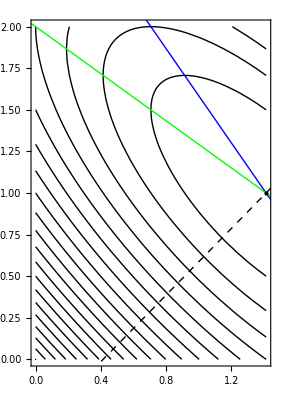

```mathematica
Grid[Map[PlotCell,Reverse[Transpose[solver[["Cells"]]]],{2}]]
```